Hamiltonian Simulation H=Z

§4.7 Simulation of quantum systems, Nielsen & Chuang

Notebook: Óscar Amaro, July 2021+August 2022 @ GoLP-EPP
Contact: oscar.amaro@tecnico.ulisboa.pt

Introduction
Quantum circuit for simulating the Hamiltonian H=⊗Z for time Δt.
Get the Quantum Mathematica package at https://homepage.cem.itesm.mx/lgomez/

- Structure of H=⊗Z for time Δt, operator and matrix form
- Equivalence between circuits with CNOT connected directly to the last/ancilla qubit or with intermediate connections (both forms are used in the literature)

```mathematica
(* import package *)
Needs["Quantum`Computing`"];
```

SetQuantumGate::shdw: Symbol SetQuantumGate appears in multiple contexts {Quantum`Computing`,Global`}; definitions in context Quantum`Computing` may shadow or be shadowed by other definitions.

## n=1

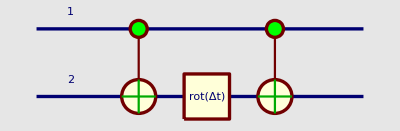

U1={{ⅇ^(-ⅈ Δt),0,0,0},{0,ⅇ^(-ⅈ Δt),0,0},{0,0,ⅇ^(ⅈ Δt),0},{0,0,0,ⅇ^(ⅈ Δt)}}

U2={{ⅇ^(-ⅈ Δt),0,0,0},{0,ⅇ^(ⅈ Δt),0,0},{0,0,ⅇ^(ⅈ Δt),0},{0,0,0,ⅇ^(-ⅈ Δt)}}

ψ={a[0],0,a[1],0}

{1,1,1,1}

```mathematica
Clear[Δt,I2,Z,RZ,U1,U2,rot,psi]
I2=PauliMatrix[0];
Z=PauliMatrix[3];

(* direct method *)
U1=MatrixExp[-I KroneckerProduct[Z,I2]Δt];

(* define Rz rotation *)
SetQuantumGate[rot,1,
Function[{q1},
Function[{Δt},
ⅇ^(-ⅈ Δt)|Subscript[0, OverHat[q1]]⟩·⟨Subscript[0, OverHat[q1]]|+ⅇ^(+ⅈ Δt)|Subscript[1, OverHat[q1]]⟩·⟨Subscript[1, OverHat[q1]]| ] ] ];
QuantumTableForm[Subscript[rot, OverHat[1]][Δt]];
QuantumMatrixForm[Subscript[rot, OverHat[1]][Δt]];
QuantumMatrixForm[(𝒞^{OverHat[3]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]];

(* build circuit *)
circ=(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[rot, OverHat[2]][Δt]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]];
(* plot *)
QuantumPlot[circ]
U2=QuantumMatrix[circ];
(* compare unitaries *)
Print["U1=",U1]
Print["U2=",U2]
(* define test ket. We are only interested on the effect of the operators on an arbitrary ket (where the ancilla is supposed to start as 0) *)
psi=ArrayFlatten[KroneckerProduct[{a[0],a[1]},{1,0}],1];
Print["ψ=",psi]
(* the non-zero entries of this ket will select the relevant entries of the operators *)
(* because of zero entries in U1,U2, we need to add ϵ to the operators and then take the limit ϵ->0 *)
Limit[(U1.psi+ϵ)/(U2.psi+ϵ),ϵ->0]
(* the resulting kets are the same *)
```

## n=2

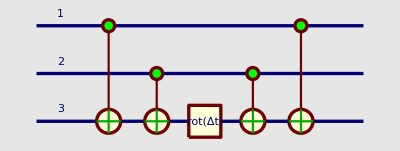

{1,1,1,1,1,1,1,1}

```mathematica
Clear[Δt,I2,Z,RZ,U1,U2,rot,psi]
I2=PauliMatrix[0];
Z=PauliMatrix[3];

(* direct method *)
U1=MatrixExp[-I KroneckerProduct[Z,Z,I2]Δt];

(* define Rz rotation *)
SetQuantumGate[rot,1,
Function[{q1},
Function[{Δt},
ⅇ^(-ⅈ Δt)|Subscript[0, OverHat[q1]]⟩·⟨Subscript[0, OverHat[q1]]|+ⅇ^(+ⅈ Δt)|Subscript[1, OverHat[q1]]⟩·⟨Subscript[1, OverHat[q1]]| ] ] ];
QuantumTableForm[Subscript[rot, OverHat[1]][Δt]];
QuantumMatrixForm[Subscript[rot, OverHat[1]][Δt]];
QuantumMatrixForm[(𝒞^{OverHat[3]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]];

(* build circuit *)
circ=(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·Subscript[rot, OverHat[3]][Δt]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[3]]];
(* plot *)
QuantumPlot[circ]
U2=QuantumMatrix[circ];
(* compare unitaries *)
psi=ArrayFlatten[KroneckerProduct[{a[0],a[1]},{a[2],a[3]},{1,0}],1];
Limit[(U1.psi+ϵ)/(U2.psi+ϵ),ϵ->0]
```

## n=3

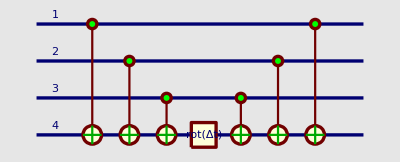

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Clear[Δt,I2,Z,RZ,U1,U2,psi]
I2=PauliMatrix[0];
Z=PauliMatrix[3];

(* direct method *)
U1=MatrixExp[-I KroneckerProduct[Z,Z,Z,I2]Δt];

(* define Rz rotation *)
SetQuantumGate[rot,1,
Function[{q1},
Function[{Δt},
ⅇ^(-ⅈ Δt)|Subscript[0, OverHat[q1]]⟩·⟨Subscript[0, OverHat[q1]]|+ⅇ^(+ⅈ Δt)|Subscript[1, OverHat[q1]]⟩·⟨Subscript[1, OverHat[q1]]| ] ] ];
QuantumTableForm[Subscript[rot, OverHat[1]][Δt]];
QuantumMatrixForm[Subscript[rot, OverHat[1]][Δt]];
QuantumMatrixForm[(𝒞^{OverHat[3]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]];

(* build circuit *)
circ=(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]·(𝒞^{OverHat[3]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]·Subscript[rot, OverHat[4]][Δt]·(𝒞^{OverHat[3]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[4]]];

(* plot *)
QuantumPlot[circ]
U2=QuantumMatrix[circ];
(* compare unitaries *)
psi=ArrayFlatten[KroneckerProduct[{a[0],a[1]},{a[2],a[3]},{a[4],a[5]},{1,0}],1];
Limit[(U1.psi+ϵ)/(U2.psi+ϵ),ϵ->0]
```

## Equivalence between circuits with CNOT connected directly to the ancilla qubit or with intermediate connections

## n=2

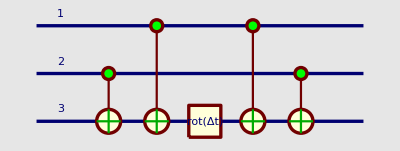

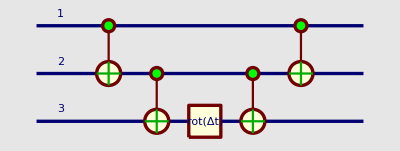

{1,1,1,1,1,1,1,1}

```mathematica
Clear[Δt,I2,Z,RZ,U1,U2,rot,psi,circ1,circ2]

I2=PauliMatrix[0];
Z=PauliMatrix[3];
(* define Rz rotation *)
SetQuantumGate[rot,1,
Function[{q1},
Function[{Δt},
ⅇ^(-ⅈ Δt)|Subscript[0, OverHat[q1]]⟩·⟨Subscript[0, OverHat[q1]]|+ⅇ^(+ⅈ Δt)|Subscript[1, OverHat[q1]]⟩·⟨Subscript[1, OverHat[q1]]| ] ] ];

(* build circuit *)
circ1=(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·Subscript[rot, OverHat[3]][Δt]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[3]]];
circ2=(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·Subscript[rot, OverHat[3]][Δt]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]];

(* plot *)
QuantumPlot[circ1]
QuantumPlot[circ2]
U1=QuantumMatrix[circ1];
U2=QuantumMatrix[circ2];
(* compare unitaries *)
psi=ArrayFlatten[KroneckerProduct[{a[0],a[1]},{a[2],a[3]},{1,0}],1];
Limit[(U1.psi+ϵ)/(U2.psi+ϵ),ϵ->0]
```

## n=3

-Graphics-

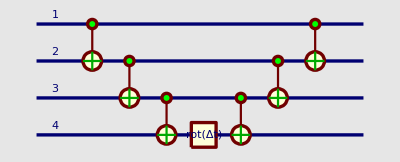

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Clear[Δt,I2,Z,RZ,U1,U2,rot,psi,circ1,circ2]

I2=PauliMatrix[0];
Z=PauliMatrix[3];
(* define Rz rotation *)
SetQuantumGate[rot,1,
Function[{q1},
Function[{Δt},
ⅇ^(-ⅈ Δt)|Subscript[0, OverHat[q1]]⟩·⟨Subscript[0, OverHat[q1]]|+ⅇ^(+ⅈ Δt)|Subscript[1, OverHat[q1]]⟩·⟨Subscript[1, OverHat[q1]]| ] ] ];

(* build circuit *)
circ1=(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]·(𝒞^{OverHat[3]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]·Subscript[rot, OverHat[4]][Δt]·(𝒞^{OverHat[3]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[4]]];
circ2=(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·(𝒞^{OverHat[3]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]·Subscript[rot, OverHat[4]][Δt]·(𝒞^{OverHat[3]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]];

(* plot *)
QuantumPlot[circ1]
QuantumPlot[circ2]
U1=QuantumMatrix[circ1];
U2=QuantumMatrix[circ2];
(* compare unitaries *)
psi=ArrayFlatten[KroneckerProduct[{a[0],a[1]},{a[2],a[3]},{a[4],a[5]},{1,0}],1];
Limit[(U1.psi+ϵ)/(U2.psi+ϵ),ϵ->0]
```

## ZZ operations in different pairs of qubits commute -> there is no specific order for the ZZ operations

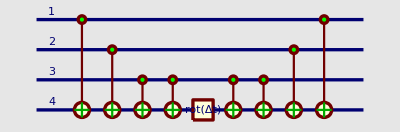

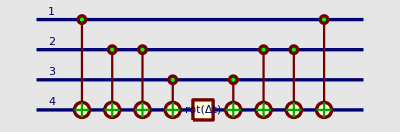

0

```mathematica
Clear[Δt,I2,Z,RZ,U1,U2,psi]
(* define Rz rotation *)
SetQuantumGate[rot,1,
Function[{q1},
Function[{Δt},
ⅇ^(-ⅈ Δt)|Subscript[0, OverHat[q1]]⟩·⟨Subscript[0, OverHat[q1]]|+ⅇ^(+ⅈ Δt)|Subscript[1, OverHat[q1]]⟩·⟨Subscript[1, OverHat[q1]]| ] ] ];

(* build circuit *)
circ12=(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]·(𝒞^{OverHat[3]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]·(𝒞^{OverHat[3]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]·Subscript[rot, OverHat[4]][Δt]·(𝒞^{OverHat[3]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]·(𝒞^{OverHat[3]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[4]]];
circ13=(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]·(𝒞^{OverHat[3]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]·Subscript[rot, OverHat[4]][Δt]·(𝒞^{OverHat[3]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[4]]];

(* plot *)
QuantumPlot[circ12]
U12=QuantumMatrix[circ12];
QuantumPlot[circ13]
U13=QuantumMatrix[circ13];

(* commutator is zero *)
Abs[U12.U13-U13.U12]//Total//Total
```

## Procedurally building a circuit implementing the k^2 operator

rot_OverHat[1][π/2]·rot_OverHat[2][π/4]·rot_OverHat[3][π/8]·rot_OverHat[4][π/16]·𝒞^{OverHat[1]}[𝒩𝒪𝒯_OverHat[5]]·𝒞^{OverHat[2]}[𝒩𝒪𝒯_OverHat[5]]·rot_OverHat[5][2 π]·𝒞^{OverHat[2]}[𝒩𝒪𝒯_OverHat[5]]·𝒞^{OverHat[1]}[𝒩𝒪𝒯_OverHat[5]^2]·𝒞^{OverHat[3]}[𝒩𝒪𝒯_OverHat[5]]·rot_OverHat[5][π]·𝒞^{OverHat[3]}[𝒩𝒪𝒯_OverHat[5]]·𝒞^{OverHat[1]}[𝒩𝒪𝒯_OverHat[5]^2]·𝒞^{OverHat[4]}[𝒩𝒪𝒯_OverHat[5]]·rot_OverHat[5][π/2]·𝒞^{OverHat[4]}[𝒩𝒪𝒯_OverHat[5]]·𝒞^{OverHat[1]}[𝒩𝒪𝒯_OverHat[5]]·𝒞^{OverHat[2]}[𝒩𝒪𝒯_OverHat[5]]·𝒞^{OverHat[3]}[𝒩𝒪𝒯_OverHat[5]]·rot_OverHat[5][π/2]·𝒞^{OverHat[3]}[𝒩𝒪𝒯_OverHat[5]]·𝒞^{OverHat[2]}[𝒩𝒪𝒯_OverHat[5]^2]·𝒞^{OverHat[4]}[𝒩𝒪𝒯_OverHat[5]]·rot_OverHat[5][π/4]·𝒞^{OverHat[4]}[𝒩𝒪𝒯_OverHat[5]]·𝒞^{OverHat[2]}[𝒩𝒪𝒯_OverHat[5]]·𝒞^{OverHat[3]}[𝒩𝒪𝒯_OverHat[5]]·𝒞^{OverHat[4]}[𝒩𝒪𝒯_OverHat[5]]·rot_OverHat[5][π/8]·𝒞^{OverHat[4]}[𝒩𝒪𝒯_OverHat[5]]·𝒞^{OverHat[3]}[𝒩𝒪𝒯_OverHat[5]]

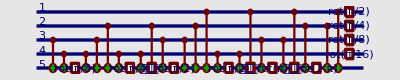

```mathematica
(* agrees with Figure 4.3 of Eltohfa "Quantum Simulation of Schrödinger's Equation" *)
Clear[Δt,I2,Z,RZ,U1,U2,psi,n,circ]

n=4;
Δt=π;

(* define Rz rotation *)
SetQuantumGate[rot,1,
Function[{q1},
Function[{Δt},
ⅇ^(-ⅈ Δt)|Subscript[0, OverHat[q1]]⟩·⟨Subscript[0, OverHat[q1]]|+ⅇ^(+ⅈ Δt)|Subscript[1, OverHat[q1]]⟩·⟨Subscript[1, OverHat[q1]]| ] ] ];

cnot[i_,j_]:=Module[{},
Return[(𝒞^{î})[Subscript[𝒩𝒪𝒯, OverHat[n+1]]]·(𝒞^{ĵ})[Subscript[𝒩𝒪𝒯, OverHat[n+1]]]·Subscript[rot, OverHat[n+1]][2^(4-i-j)Δt]·(𝒞^{ĵ})[Subscript[𝒩𝒪𝒯, OverHat[n+1]]]·(𝒞^{î})[Subscript[𝒩𝒪𝒯, OverHat[n+1]]]]
]

circ=⊗_(j=1)^n Subscript[rot, ĵ][2^(-n+4-j)Δt]·⊗_(j=1)^n ⊗_(m=j+1)^n cnot[j,m]
QuantumPlot[circ]
```